```mathematica
f[123]
```

f[123]

```mathematica
Hold[FullForm[a = 1.0;
b = 2.0;
a + b]]
```

Hold[CompoundExpression[Set[a,1.],Set[b,2.],Plus[a,b]]]

```mathematica
a = 1.0;
b = 2.0;
a + b
```

3.

```mathematica
Hold[FullForm[a = 1.0;
b = 2.0;
a + b;]]
```

Hold[CompoundExpression[Set[a,1.],Set[b,2.],Plus[a,b],Null]]

```mathematica
Null
```

```mathematica
a=1
```

1

```mathematica
Hold[FullForm[a = 1]]
```

Hold[Set[a,1]]

```mathematica
a=1;
```

```mathematica
Hold[FullForm[a = 1;]]
```

Hold[CompoundExpression[Set[a,1],Null]]

```mathematica
a = 123;
b = 321;
```

```mathematica
Print[{a , b}]
```

{123,321}

```mathematica
a = 1.0;
b = 2.0;
a + b
```

3.

```mathematica
Print[{a , b}]
```

{1.,2.}

```mathematica
a = 123;
b = 321;
```

```mathematica
Module[{a , b},
a = 1.0;
b = 2.0;
a+b]
```

3.

```mathematica
Print[{a , b}]
```

{123,321}

```mathematica
Hold[FullForm[Module[{a , b},
a = 1.0;
b = 2.0;
a+b]]]
```

Hold[Module[List[a,b],CompoundExpression[Set[a,1.],Set[b,2.],Plus[a,b]]]]

```mathematica
Module[{a =1.0, b=2.0},
a+b]
```

3.

```mathematica
Hold[FullForm[Module[{a =1.0, b=2.0},
a+b]]]
```

Hold[Module[List[Set[a,1.],Set[b,2.]],Plus[a,b]]]

```mathematica
FullForm[Plot[Sin[x] , {x , -π , π}]];
```

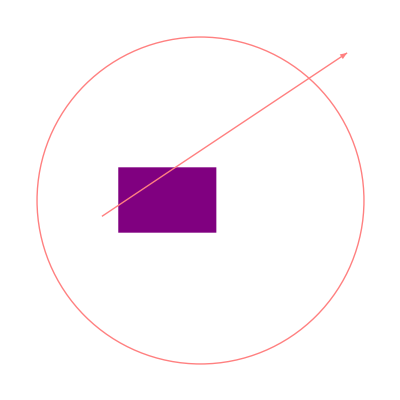

```mathematica
Graphics[
{
Pink ,
Thick, 
Circle[{0. , 0.} , 1.], 
{
Purple , 
Rectangle[{-0.5 , -0.2},{0.1 , 0.2}]
},
Arrow[{{-0.6 , -0.1},{0.9 , 0.9}}]
}
]
```

```mathematica
Clear[a , b];
```

```mathematica
a={{a11 , a12},{a21 , a22}};
```

```mathematica
b ={{b11 , b12} , {b21 , b22}};
```

```mathematica
MatrixForm[a]
```

(a11 | a12
a21 | a22)

```mathematica
MatrixForm[b]
```

(b11 | b12
b21 | b22)

```mathematica
MatrixForm[α a]
```

(a11 α | a12 α
a21 α | a22 α)

```mathematica
MatrixForm[a + b]
```

(a11+b11 | a12+b12
a21+b21 | a22+b22)

```mathematica
MatrixForm[a + b + a]
```

(2 a11+b11 | 2 a12+b12
2 a21+b21 | 2 a22+b22)

```mathematica
MatrixForm[a.b]
```

(a11 b11+a12 b21 | a11 b12+a12 b22
a21 b11+a22 b21 | a21 b12+a22 b22)

```mathematica
Hold[FullForm[a.b]]
```

Hold[Dot[a,b]]

```mathematica
(*ESC ii ESC*)
```

```mathematica
(*x + y ⅈ*)
```

```mathematica
ⅈ ⅈ
```

-1

```mathematica
{x , y}
```

{x,y}

```mathematica
solution=Solve[(x + 1)(x + 2)==0 , {x}];
```

```mathematica
solution
```

{{x→-2},{x→-1}}

```mathematica
x/.solution[[1]]
```

-2

```mathematica
Hold[FullForm[x/.solution[[1]]]]
```

Hold[ReplaceAll[x,Part[solution,1]]]

```mathematica
(*- >*)
```

```mathematica
mojeParametry={parametr1 ->3 , parametr2->10 , kat->π/10};
```

```mathematica
f[parametr1 kat]/.mojeParametry
```

f[(3 π)/10]

```mathematica
solution
```

{{x→-2},{x→-1}}

```mathematica
x/.solution
```

{-2,-1}

```mathematica
solution[[1]]
```

{x→-2}

```mathematica
x/.solution[[1]]
```

-2

```mathematica
(*inaczej niż mul[x_ , y_]:=x y*)
```

```mathematica
mul[x_][y_]:=x y;
```

```mathematica
mul[2][3]
```

6

```mathematica
mulByThree = mul[3];
```

```mathematica
mulByThree[6]
```

18

```mathematica
mul[3]
```

mul[3]

```mathematica
mulByThree
```

mul[3]

```mathematica
f[c_][z_]:=z+c;
```

```mathematica
k[n_][c_]:=Nest[f[c] , 1.0 , n];
```

```mathematica
fiveIterations = k[5];
```

```mathematica
fiveIterations[2.0 + 3.0 ⅈ]
```

11.+15. ⅈ

```mathematica
Abs[%]
```

18.6011

```mathematica
Sqrt[11^2 + 15^2]//N
```

18.6011

```mathematica
fiveIterations[]
```

k[5][]

```mathematica
Sin[2.]
```

0.909297

```mathematica
lsakmda[1. , 3. , 4.]
```

lsakmda[1.,3.,4.]